```mathematica
Manipulate[Plot[{Sqrt[(1/2)*r^2+Sqrt[(1/4)r^4+4x^2]]},{x,-0.05,0.05},PlotRange->{{-0.005,0.005},{0,0.06}},AspectRatio->0.6],{r,0,0.05,0.005}]
```

```mathematica
Table[ParametricPlot[{((1+2*m*Cos[2*theta]+m^2)^-1)*(1-m^2)*((1+m^2)^-0.5)*(1-m)*Sin[theta]*Sqrt[2],((1+2*m*Cos[2*theta]+m^2)^-1)*(1-m^2)*((1+m^2)^-0.5)*(1+m)*Cos[theta]*Sqrt[2]},{theta,0,2Pi},PlotRange->{{-0.005,0.005},{0,0.06}},AspectRatio->0.6],{m,0.99,0.95,0.01}]
```

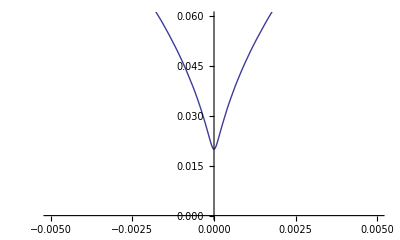

```mathematica
m=0.9801970394328878;
Y[theta_]:=((1+2*m*Cos[2*theta]+m^2)^-1)*(1-m^2)*((1+m^2)^-0.5)*(1+m)*Cos[theta]*Sqrt[2]
X[theta_]:=((1+2*m*Cos[2*theta]+m^2)^-1)*(1-m^2)*((1+m^2)^-0.5)*(1-m)*Sin[theta]*Sqrt[2]
a=ParametricPlot[{X[theta],Y[theta]},{theta,0,2Pi},PlotRange->{{-0.005,0.005},{0,0.06}},AspectRatio->0.6]
```

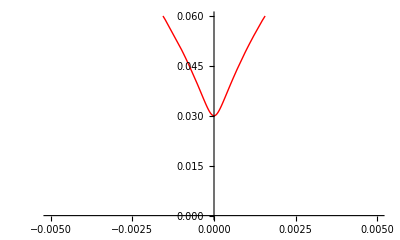

```mathematica
r=0.03;
b=Plot[{Sqrt[(1/2)*r^2+Sqrt[(1/4)r^4+4x^2]]},{x,-0.05,0.05},PlotRange->{{-0.005,0.005},{0,0.06}},AspectRatio->0.6,PlotStyle->{Red,Thick}]
```

### HOPPERS SOLUTION

```mathematica
HOPPERS SOLUTION
Clear[x]
Clear[y]
Clear[m]
L[m_]:=2*(1-m^2)^2/(1+m^2)
K[y_]:=(y^2*L[m])/((1+m)*(x^2+y^2))^2+(x^2*L[m])/((1-m)*(x^2+y^2))^2
P[m_]:=(y^2*L[m])/((1+m)*(x^2+y^2))^2+(x^2*L[m])/((1-m)*(x^2+y^2))^2
x=0;
y=0.134821;
Solve[P[m]==1,m]
```

HOPPERS SOLUTION

{{m→0.873424},{m→1.14492}}

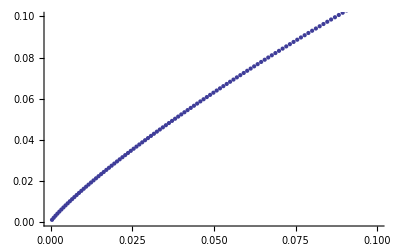

```mathematica
hoprt=ListPlot[AA,PlotRange->{{0,0.1},{0,0.1}}]
```

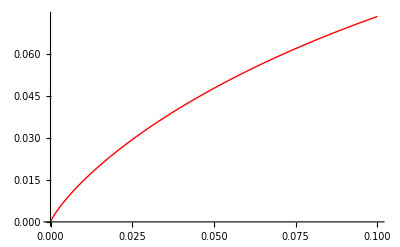

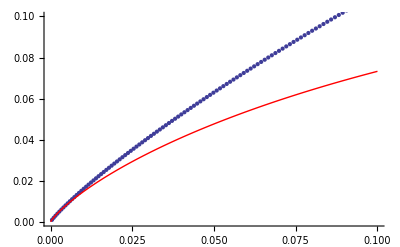

```mathematica
egrt=Plot[(-1/Pi)*t*Log[t],{t,0.00001,0.1},PlotStyle->Red]
```

```mathematica
Dimensions[AA]
```

{500,2}

```mathematica
R=Interpolation[AA]
```

InterpolatingFunction[{{0.000449067,1.17393}},<>]

```mathematica
RV=Table[{R[x],R'[x]},{x,0.001,0.4,0.001}];
```

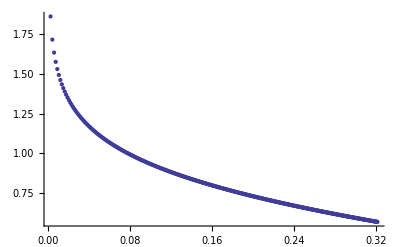

```mathematica
aa=ListPlot[RV]
```

```mathematica
bb=Plot[(-1/(2*Pi))*Log[r^2],{r,0.000001,0.5},PlotStyle->{Thick,Green},PlotRange->All];
```

```mathematica
bb1=Plot[(-1/(2*Pi))*Log[del[r]/r],{r,0.001,0.5},PlotStyle->{Thick,Red},PlotRange->All];
```

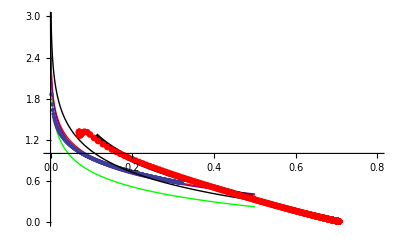

```mathematica
bb2=Plot[(-1/(2*Pi))*Log[0.31*(r^2)],{r,0.000001,0.5},PlotStyle->{Purple,Thick},PlotRange->All];
bb3=Plot[(-Sqrt[2]/(2*Pi))*Log[(r^2)],{r,0.000001,0.5},PlotStyle->{Black,Thick},PlotRange->All];
Show[bb,bb1,bb2,aa,bb3,vb5,va,PlotRange->{{0,0.8},{0,3}}]
```

```mathematica
h[x_]=√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2))/.m->0.9417221058682982
```

0.06

```mathematica
h[x]
```

√(-x^2+2 √(x^2))

```mathematica
YY=Table[0.001+0.001*i,{i,0,500}];
t=0;
M=Table[FindRoot[(YY[[i]]^2*(2*(1-m^2)^2/(1+m^2)))/((1+m)*(t^2+YY[[i]]^2))^2+(t^2*(2*(1-m^2)^2/(1+m^2)))/((1-m)*(t^2+YY[[i]]^2))^2==1,{m,0,1}],{i,1,Dimensions[YY][[1]]}];
FF=Table[√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-(x-1)^2/(1+m^2)-(m^2 (x-1)^2)/(1+m^2)+1/(1+m^2) (√(1-4 m+6 m^2-4 m^3+m^4+8 m (x-1)^2+8 m^3 (x-1)^2)))/.M[[i]],{i,1,Dimensions[YY][[1]]}];
```

```mathematica
DeltaHopper=Table[{FF[[i]]/.x->1,1/(((D[FF[[i]],{x,2}]-(D[FF[[i]],{x,1}])^2/(FF[[i]])-1/(FF[[i]]))*((1+(D[FF[[i]],{x,1}])^2)^-1.5)/.x->1))},{i,1,Dimensions[YY][[1]]}];
DeltaHopper1=Table[{FF[[i]]/.x->1,1/D[FF[[i]],{x,2}]/.x->1},{i,1,Dimensions[YY][[1]]}];
```

```mathematica
del=Interpolation[DeltaHopper]
```

InterpolatingFunction[{{0.000999928,0.501}},<>]

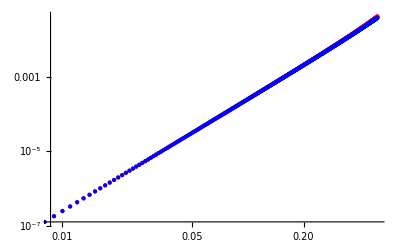

```mathematica
HOP=ListLogLogPlot[{DeltaHopper,DeltaHopper1},PlotStyle->{Red,Blue}]
```

```mathematica
Export["DeltaHopper.txt",DeltaHopper,"Table"]
```

DeltaHopper.txt

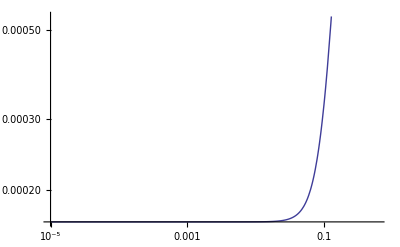

```mathematica
Hopperfit=LogLogPlot[a*(x^b)+c/.{a->0.441192,b->3.42816,c->0.000166256},{x,0.00001,0.6},PlotStyle->Thick]
```

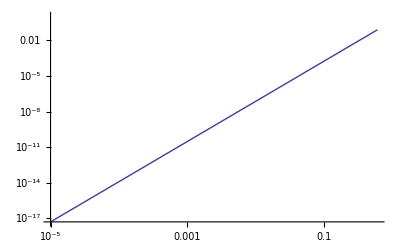

```mathematica
Hopperfit=LogLogPlot[a*(x^b)+c/.{a->0.428691,b->3.38434,c->0},{x,0.00001,0.6},PlotStyle->Thick]
```

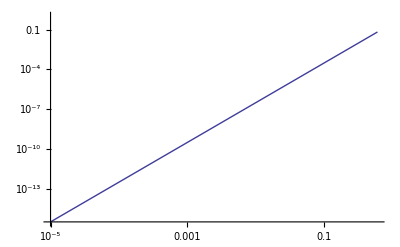

```mathematica
Hopperfit=LogLogPlot[a*(x^b)+c/.{a->0.311708,b->3,c->0},{x,0.00001,0.6},PlotStyle->Thick]
```

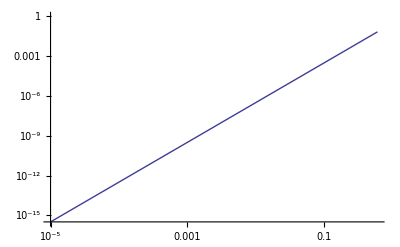

```mathematica
Hopperfit=LogLogPlot[a*(x^b)+c/.{a->0.319397,b->3,c->0},{x,0.00001,0.6},PlotStyle->Thick]
```

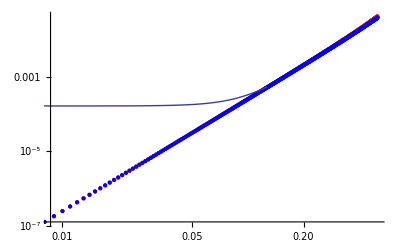

```mathematica
Show[HOP,Hopperfit]
```

```mathematica
Table[{fma06[[i]][1],(((fma06[[i]]''[1]-(fma06[[i]]'[1])^2/(fma06[[i]][1])-1)*((1+(fma06[[i]]'[1])^2)^-1.5)))},{i,1,NNma06}];
```

```mathematica
h'[0]
```

0

```mathematica
h''[0]
```

357.688

```mathematica
Sqrt[2]*(1-m)*1/(Sqrt[1+m^2])/.{m->1}
```

0

```mathematica
h[0]
```

0

```mathematica
ArcSin[Sqrt[0.5]]
```

0.785398

```mathematica
Sin[Pi/2]
```

1

```mathematica
*Sqrt[1+miu]
```

```mathematica
*(Integrate[1/Sqrt[(1-miu*Sin[theta]*Sin[theta])],{theta,0,Pi/2}])
```

```mathematica
Clear[x]
h[x_]=√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2))/.m->0.8734236546984816
```

√(0.00908835-1. x^2+0.567257 √(0.000256691+12.3179 x^2))

```mathematica
Manipulate[Plot[√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2)),{x,-1,0},PlotRange->{{-1,0},{0,2}},AspectRatio->0.6],{m,0,0.9,0.1}]
```

```mathematica
-0.9999999999999998
```

```mathematica
AA
```

{{0.000449067,0.0010005},{0.000967114,0.002002},{0.00151941,0.0030045},{0.00209681,0.00400801},{0.00269463,0.00501252},{0.00330993,0.00601803},{0.0039407,0.00702454},{0.00458546,0.00803206},{0.00524306,0.00904059},{0.0059126,0.0100501},{0.00659334,0.0110607},{0.00728465,0.0120722},{0.00798601,0.0130848},{0.00869698,0.0140983},{0.00941716,0.0151129},{0.0101462,0.0161285},{0.0108838,0.0171451},{0.0116297,0.0181627},{0.0123837,0.0191813},{0.0131455,0.020201},{0.013915,0.0212216},{0.0146919,0.0222433},{0.0154761,0.023266},{0.0162674,0.0242897},{0.0170658,0.0253144},{0.017871,0.0263402},{0.018683,0.0273669},{0.0195017,0.0283947},{0.0203269,0.0294235},{0.0211585,0.0304533},{0.0219966,0.0314842},{0.0228409,0.032516},{0.0236914,0.0335489},{0.024548,0.0345828},{0.0254108,0.0356178},{0.0262795,0.0366537},{0.0271541,0.0376907},{0.0280347,0.0387287},{0.028921,0.0397678},{0.0298132,0.0408078},{0.0307111,0.0418489},{0.0316146,0.0428911},{0.0325238,0.0439342},{0.0334386,0.0449784},{0.034359,0.0460236},{0.0352849,0.0470699},{0.0362163,0.0481171},{0.0371531,0.0491655},{0.0380954,0.0502148},{0.0390431,0.0512652},{0.0399961,0.0523166},{0.0409545,0.0533691},{0.0419182,0.0544226},{0.0428872,0.0554771},{0.0438614,0.0565327},{0.0448409,0.0575893},{0.0458257,0.0586469},{0.0468156,0.0597056},{0.0478107,0.0607653},{0.048811,0.0618261},{0.0498165,0.0628879},{0.0508271,0.0639508},{0.0518428,0.0650147},{0.0528636,0.0660796},{0.0538895,0.0671456},{0.0549205,0.0682126},{0.0559566,0.0692807},{0.0569977,0.0703498},{0.0580439,0.07142},{0.0590951,0.0724912},{0.0601514,0.0735635},{0.0612126,0.0746368},{0.0622789,0.0757111},{0.0633502,0.0767865},{0.0644265,0.077863},{0.0655078,0.0789405},{0.066594,0.0800191},{0.0676853,0.0810987},{0.0687815,0.0821794},{0.0698826,0.0832611},{0.0709888,0.0843439},{0.0720999,0.0854277},{0.0732159,0.0865126},{0.0743369,0.0875985},{0.0754629,0.0886855},{0.0765938,0.0897736},{0.0777296,0.0908627},{0.0788704,0.0919529},{0.0800162,0.0930441},{0.0811669,0.0941364},{0.0823225,0.0952297},{0.083483,0.0963241},{0.0846485,0.0974196},{0.085819,0.0985162},{0.0869943,0.0996137},{0.0881746,0.100712},{0.0893599,0.101812},{0.0905501,0.102913},{0.0917453,0.104015},{0.0929454,0.105118},{0.0941504,0.106222},{0.0953604,0.107327},{0.0965753,0.108433},{0.0977953,0.10954},{0.0990201,0.110648},{0.10025,0.111758},{0.101485,0.112868},{0.102725,0.113979},{0.103969,0.115092},{0.105219,0.116205},{0.106474,0.11732},{0.107733,0.118436},{0.108998,0.119553},{0.110268,0.120671},{0.111542,0.121789},{0.112822,0.122909},{0.114107,0.124031},{0.115397,0.125153},{0.116691,0.126276},{0.117991,0.1274},{0.119296,0.128526},{0.120606,0.129652},{0.121921,0.13078},{0.123241,0.131908},{0.124566,0.133038},{0.125896,0.134169},{0.127231,0.135301},{0.128572,0.136434},{0.129917,0.137568},{0.131268,0.138703},{0.132623,0.139839},{0.133984,0.140976},{0.13535,0.142114},{0.136721,0.143254},{0.138097,0.144394},{0.139478,0.145536},{0.140865,0.146679},{0.142257,0.147822},{0.143654,0.148967},{0.145056,0.150113},{0.146463,0.15126},{0.147875,0.152408},{0.149293,0.153557},{0.150716,0.154707},{0.152144,0.155859},{0.153578,0.157011},{0.155016,0.158165},{0.15646,0.159319},{0.15791,0.160475},{0.159364,0.161632},{0.160824,0.16279},{0.162289,0.163949},{0.16376,0.165109},{0.165236,0.16627},{0.166717,0.167432},{0.168204,0.168595},{0.169696,0.16976},{0.171193,0.170925},{0.172696,0.172092},{0.174204,0.173259},{0.175718,0.174428},{0.177237,0.175598},{0.178761,0.176769},{0.180291,0.177941},{0.181827,0.179114},{0.183368,0.180288},{0.184914,0.181463},{0.186466,0.18264},{0.188024,0.183817},{0.189587,0.184996},{0.191155,0.186176},{0.19273,0.187356},{0.194309,0.188538},{0.195895,0.189721},{0.197486,0.190905},{0.199083,0.19209},{0.200685,0.193277},{0.202293,0.194464},{0.203907,0.195652},{0.205526,0.196842},{0.207151,0.198032},{0.208782,0.199224},{0.210418,0.200417},{0.212061,0.201611},{0.213709,0.202806},{0.215362,0.204002},{0.217022,0.205199},{0.218688,0.206398},{0.220359,0.207597},{0.222036,0.208798},{0.223719,0.209999},{0.225408,0.211202},{0.227103,0.212406},{0.228803,0.213611},{0.23051,0.214817},{0.232223,0.216024},{0.233941,0.217232},{0.235666,0.218441},{0.237396,0.219652},{0.239133,0.220863},{0.240876,0.222076},{0.242624,0.223289},{0.244379,0.224504},{0.24614,0.22572},{0.247907,0.226937},{0.24968,0.228155},{0.251459,0.229374},{0.253244,0.230595},{0.255036,0.231816},{0.256834,0.233039},{0.258638,0.234262},{0.260448,0.235487},{0.262264,0.236713},{0.264087,0.23794},{0.265916,0.239168},{0.267752,0.240397},{0.269593,0.241627},{0.271442,0.242858},{0.273296,0.244091},{0.275157,0.245324},{0.277024,0.246559},{0.278898,0.247795},{0.280778,0.249032},{0.282665,0.250269},{0.284558,0.251509},{0.286458,0.252749},{0.288364,0.25399},{0.290277,0.255232},{0.292196,0.256476},{0.294122,0.25772},{0.296055,0.258966},{0.297994,0.260213},{0.29994,0.261461},{0.301893,0.26271},{0.303852,0.26396},{0.305819,0.265211},{0.307792,0.266463},{0.309771,0.267716},{0.311758,0.268971},{0.313751,0.270226},{0.315751,0.271483},{0.317759,0.272741},{0.319773,0.274},{0.321794,0.27526},{0.323821,0.276521},{0.325856,0.277783},{0.327898,0.279046},{0.329947,0.280311},{0.332003,0.281576},{0.334066,0.282843},{0.336136,0.28411},{0.338214,0.285379},{0.340298,0.286649},{0.34239,0.28792},{0.344488,0.289192},{0.346594,0.290465},{0.348708,0.29174},{0.350828,0.293015},{0.352956,0.294291},{0.355091,0.295569},{0.357234,0.296848},{0.359384,0.298128},{0.361541,0.299408},{0.363706,0.30069},{0.365878,0.301973},{0.368058,0.303258},{0.370245,0.304543},{0.37244,0.305829},{0.374642,0.307117},{0.376852,0.308405},{0.37907,0.309695},{0.381295,0.310986},{0.383528,0.312278},{0.385769,0.313571},{0.388017,0.314865},{0.390274,0.31616},{0.392538,0.317456},{0.394809,0.318753},{0.397089,0.320052},{0.399377,0.321351},{0.401672,0.322652},{0.403976,0.323954},{0.406287,0.325256},{0.408607,0.32656},{0.410934,0.327865},{0.41327,0.329171},{0.415614,0.330478},{0.417965,0.331787},{0.420325,0.333096},{0.422694,0.334406},{0.42507,0.335718},{0.427455,0.337031},{0.429848,0.338344},{0.432249,0.339659},{0.434659,0.340975},{0.437077,0.342292},{0.439503,0.34361},{0.441938,0.344929},{0.444382,0.346249},{0.446834,0.347571},{0.449295,0.348893},{0.451764,0.350217},{0.454241,0.351541},{0.456728,0.352867},{0.459223,0.354194},{0.461727,0.355521},{0.46424,0.35685},{0.466761,0.35818},{0.469292,0.359511},{0.471831,0.360843},{0.474379,0.362177},{0.476936,0.363511},{0.479502,0.364846},{0.482077,0.366183},{0.484661,0.36752},{0.487254,0.368859},{0.489857,0.370199},{0.492468,0.371539},{0.495089,0.372881},{0.497719,0.374224},{0.500358,0.375568},{0.503007,0.376913},{0.505665,0.378259},{0.508332,0.379607},{0.511009,0.380955},{0.513695,0.382304},{0.516391,0.383655},{0.519096,0.385006},{0.521811,0.386359},{0.524536,0.387712},{0.52727,0.389067},{0.530014,0.390423},{0.532768,0.39178},{0.535532,0.393138},{0.538305,0.394497},{0.541089,0.395857},{0.543882,0.397218},{0.546685,0.39858},{0.549498,0.399943},{0.552322,0.401307},{0.555155,0.402673},{0.557999,0.404039},{0.560853,0.405407},{0.563717,0.406775},{0.566591,0.408145},{0.569476,0.409515},{0.572371,0.410887},{0.575276,0.41226},{0.578192,0.413634},{0.581118,0.415008},{0.584055,0.416384},{0.587003,0.417761},{0.589961,0.419139},{0.59293,0.420518},{0.59591,0.421898},{0.5989,0.42328},{0.601902,0.424662},{0.604914,0.426045},{0.607937,0.427429},{0.610971,0.428815},{0.614016,0.430201},{0.617073,0.431588},{0.62014,0.432977},{0.623219,0.434366},{0.626308,0.435757},{0.629409,0.437148},{0.632522,0.438541},{0.635646,0.439935},{0.638781,0.441329},{0.641928,0.442725},{0.645086,0.444122},{0.648256,0.44552},{0.651438,0.446918},{0.654631,0.448318},{0.657836,0.449719},{0.661053,0.451121},{0.664282,0.452524},{0.667523,0.453928},{0.670775,0.455333},{0.67404,0.456739},{0.677317,0.458146},{0.680606,0.459554},{0.683907,0.460963},{0.687221,0.462373},{0.690546,0.463784},{0.693884,0.465196},{0.697235,0.466609},{0.700598,0.468023},{0.703974,0.469438},{0.707362,0.470854},{0.710763,0.472272},{0.714177,0.47369},{0.717604,0.475109},{0.721043,0.476529},{0.724495,0.47795},{0.727961,0.479373},{0.731439,0.480796},{0.734931,0.48222},{0.738435,0.483645},{0.741953,0.485071},{0.745484,0.486498},{0.749029,0.487927},{0.752587,0.489356},{0.756159,0.490786},{0.759744,0.492217},{0.763343,0.493649},{0.766955,0.495082},{0.770581,0.496516},{0.774221,0.497952},{0.777875,0.499388},{0.781543,0.500825},{0.785225,0.502263},{0.788922,0.503702},{0.792632,0.505142},{0.796357,0.506583},{0.800095,0.508025},{0.803849,0.509468},{0.807617,0.510912},{0.811399,0.512356},{0.815196,0.513802},{0.819008,0.515249},{0.822834,0.516697},{0.826675,0.518146},{0.830531,0.519595},{0.834403,0.521046},{0.838289,0.522498},{0.84219,0.52395},{0.846107,0.525404},{0.850039,0.526858},{0.853986,0.528314},{0.857949,0.52977},{0.861928,0.531227},{0.865921,0.532686},{0.869931,0.534145},{0.873957,0.535605},{0.877998,0.537066},{0.882055,0.538528},{0.886129,0.539991},{0.890218,0.541455},{0.894324,0.54292},{0.898446,0.544386},{0.902584,0.545853},{0.906739,0.547321},{0.91091,0.548789},{0.915098,0.550259},{0.919303,0.551729},{0.923524,0.553201},{0.927763,0.554673},{0.932018,0.556146},{0.936291,0.55762},{0.940581,0.559095},{0.944888,0.560571},{0.949212,0.562048},{0.953554,0.563526},{0.957913,0.565005},{0.96229,0.566485},{0.966685,0.567965},{0.971097,0.569447},{0.975528,0.570929},{0.979977,0.572412},{0.984443,0.573896},{0.988928,0.575381},{0.993431,0.576867},{0.997953,0.578354},{1.00249,0.579842},{1.00705,0.58133},{1.01163,0.58282},{1.01623,0.58431},{1.02084,0.585801},{1.02548,0.587294},{1.03013,0.588787},{1.0348,0.59028},{1.0395,0.591775},{1.04421,0.593271},{1.04894,0.594767},{1.05369,0.596265},{1.05846,0.597763},{1.06325,0.599262},{1.06806,0.600762},{1.07289,0.602263},{1.07774,0.603764},{1.08262,0.605267},{1.08751,0.60677},{1.09242,0.608274},{1.09736,0.60978},{1.10231,0.611285},{1.10729,0.612792},{1.11228,0.6143},{1.1173,0.615808},{1.12234,0.617317},{1.1274,0.618828},{1.13248,0.620338},{1.13759,0.62185},{1.14271,0.623363},{1.14786,0.624876},{1.15303,0.62639},{1.15822,0.627906},{1.16344,0.629421},{1.16867,0.630938},{1.17393,0.632456}}

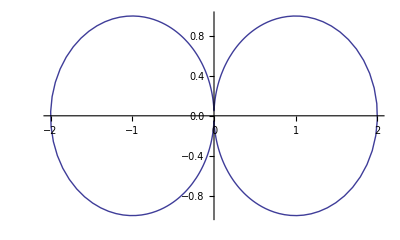

```mathematica
ParametricPlot[Table[{((1+2*m*Cos[2*theta]+m^2)^-1)*(1-m^2)*((1+m^2)^-0.5)*(1-m)*Sin[theta]*Sqrt[2],((1+2*m*Cos[2*theta]+m^2)^-1)*(1-m^2)*((1+m^2)^-0.5)*(1+m)*Cos[theta]*Sqrt[2]},{m,0.95,0.95,-0.01}],{theta,0,2Pi},PlotRange->{{-2,2},{-1,1}},AspectRatio->0.6]
```

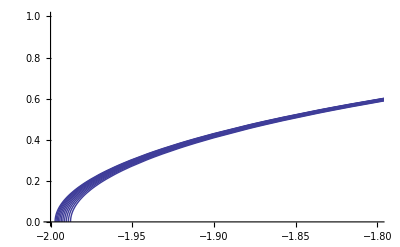

```mathematica
Plot[Table[√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2)),{m,0.9,0.8,-0.01}],{x,-2,2},PlotRange->{{-2,-1.8},{0,1}},MaxRecursion->15]
```

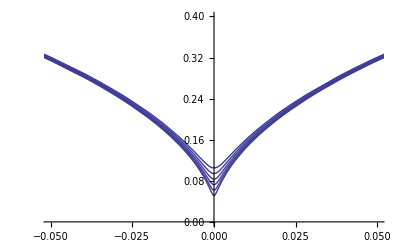

```mathematica
Plot[Table[√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2)),{m,0.95,0.90,-0.01}],{x,-2,2},PlotRange->{{-0.05,0.05},{0,0.4}},MaxRecursion->15]
```

```mathematica
(√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2))/.m->0.9)/.x->0
```

0.105118

```mathematica
√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2))/.m->0.999
```

√(5.005×10^-7-1. x^2+0.5005 √(1.00053×10^-12+15.968 x^2))

```mathematica
D[(√(1/(1+m^2)-(2 m)/(1+m^2)+m^2/(1+m^2)-x^2/(1+m^2)-(m^2 x^2)/(1+m^2)+(√(1-4 m+6 m^2-4 m^3+m^4+8 m x^2+8 m^3 x^2))/(1+m^2))/.m->0.999),{x,2}]/.x->0
```

3.99267×10^9

```mathematica
1/%
```

2.53797×10^-7